# Rotational State Distributions vs. temperatures

Sometimes, the rotational temperature is different from the thermal temperature, indicating poor thermalization into a Maxwell-Boltzmann distribution

```mathematica
B=3.3;(*0.25 for SrF*)
h=6.6*10^(-34);
c=3*10^10;
k=1.38*10^(-23);
T=6.6;
T2=50;
j=1;
ϕ=1;
```

```mathematica
ψ=h*c*B/(k*T);
Q=1+ϕ 3*E^(-2*ψ)+ϕ 5*E^(-6*ψ)+ϕ 7*E^(-20*ψ);
ψ2=h*c*B/(k*T2);
Q2=1+ϕ 3*E^(-2*ψ2)+ϕ 5*E^(-6*ψ2)+ϕ 7*E^(-12*ψ2)+ϕ 9*E^(-20*ψ2);
```

```mathematica
Clear[x]
```

```mathematica
Populations vs rotational state number _Black-> T, red ->T2
```

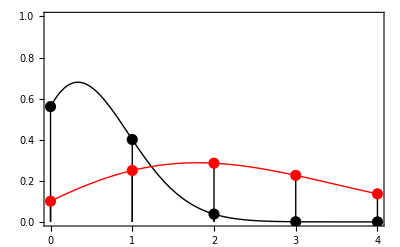

```mathematica
Show[Plot[ϕ (2x+1)*E^(-x(x+1)*ψ)/Q,{x,0,4}, PlotStyle->{Thick, Black},PlotRange->{0,1}],ListPlot[Table[{x,ϕ(2x+1)*E^(-x(x+1)*ψ)/Q},{x,0,4}], PlotStyle->{PointSize[0.02], Black},Filling->Axis,FillingStyle->Opacity[1],PlotRange->{0,1}],Plot[ϕ(2x+1)*E^(-x(x+1)*ψ2)/Q2,{x,0,4}, PlotStyle->{Thick,Red}],ListPlot[Table[{x,ϕ(2x+1)*E^(-x(x+1)*ψ2)/Q2},{x,0,4}], PlotStyle->{PointSize[0.02],Red},Filling->Axis,FillingStyle->Opacity[1],PlotRange->{0,1}],Frame->True]
```

## Populations vs. rotational temperature (Black → N=0, red → N=1)

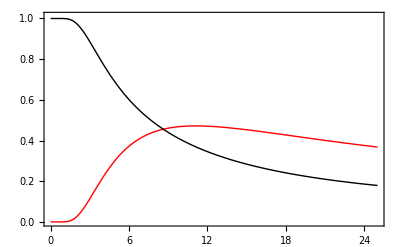

```mathematica
Show[Plot[ϕ(2j+1)*E^(-j(j+1)*h*c*B/(k*τ))/(1+3*E^(-2*h*c*B/(k*τ))+5*E^(-6*h*c*B/(k*τ))+7*E^(-12*h*c*B/(k*τ))+9*E^(-20*h*c*B/(k*τ))),{τ,0,25},PlotStyle->{Thick,Red},PlotRange->{0,1.01},Frame->True],Plot[ϕ/(1+3*E^(-2*h*c*B/(k*τ))+5*E^(-6*h*c*B/(k*τ))+7*E^(-12*h*c*B/(k*τ))+9*E^(-20*h*c*B/(k*τ))),{τ,0,25}, PlotStyle->{Thick, Black}]]
```

## junk:

```mathematica
G0=1172/2+4.
```

590.

```mathematica
E^(-h*c*G0/(k*T2))
```

4.14967×10^-19

```mathematica
1/7.
```

0.142857

```mathematica
3.3*.75*3*10^10
```

7.425×10^10

```mathematica
3.3*1.25*3*10^10-3.3*.75*3*10^10
```

4.95×10^10

```mathematica
3.3*(.75-1.25)
```

-1.65

```mathematica
3*10^8/.905*10^(-6)
```

331.492

```mathematica
25./2
```

12.5

```mathematica
11.5+1.38
```

12.88

```mathematica
12.8799*2.54
```

32.7149

```mathematica
9000/16.
```

562.5